## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW151226";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={};
mergerParams={};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dalpha_3] does not exist.

```mathematica
samples
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

## m1-m2 Plot, 22

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)
(*1. 数据提取与概率密度 (不变)*)
(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];m2Data=samples[p][[2]];
devData=samples[p][[5]];
grData=samples[p][[6]];   (*GR 系数值*)
paramData=samples[p][[7]];  (*GR*(1+d) 参数化值*)

m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

contourPD[p]={0.005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 22848 + 镜像 22848

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.005}，共 2 条

第一条前3点：{{12.3909,11.8875},{12.5267,11.7612},{12.5503,11.7395}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

```mathematica
ListLinePlot[contourPoints[p]]
```

ListLinePlot::lpn: contourPoints[p] is not a list of numbers or pairs of numbers.

ListLinePlot[contourPoints[p]]

0.831126

0.5

dphi_2 grTargets = {6.22281,6.35214}

dphi_2 paramTargets = {5.83737,6.50536}

dphi_2 GR 线有效点数：下=8 上=13

dphi_2 参数化线有效点数：下=1 上=24

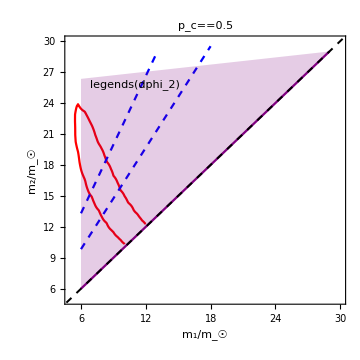

```mathematica
probability=prob
probability=0.5

(* ==========================================*)(*2. 解析参数名+计算目标值*)(* ==========================================*)
m1s=Range[5,30,1];m2s=Range[5,30,1];

pInterval=IntervalFromProbability[probability/2];

tapeIntervals["mass1"]=Quantile[m1Data,pInterval];
tapeIntervals["mass2"]=Quantile[m2Data,pInterval];

(*⭐ 解析参数名：自动拼出真实的物理函数*)
paramCore=StringDrop[p,1];  (*"dphi_2"->"phi_2"*)
{typeName,orderStr}=StringSplit[paramCore,"_"];
orderVal=If[StringEndsQ[orderStr,"l"],orderStr,ToExpression[orderStr]];
realFuncName=Symbol["IMRPhenomD"<>Capitalize[typeName]<>"NS"];

(*⭐⭐⭐ 关键修复：强制 N[] 确保目标值一定是数字 ⭐⭐⭐*)
grTargets=N[Quantile[N[grData],N[pInterval]]];     (*两个数字：{下界,上界}*)
paramTargets=N[Quantile[N[paramData],N[pInterval]]]; (*两个数字：{下界,上界}*)

(*打印验证*)
Print[p," grTargets = ",grTargets];
Print[p," paramTargets = ",paramTargets];


(* ==========================================*)
(*3. 反解（GR 和参数化用同一个公式，目标值不同）*)
(* ==========================================*)
(*物理含义：GR 线：IMRPhenomDPhiNS[2,m1,m2,0,0]==GR系数的分位数 参数化线：IMRPhenomDPhiNS[2,m1,m2,0,0]==参数化值的分位数 两者用的是同一个解析函数，区别只在目标值*)
theFormula=Function[{h,m2,c1,c2},realFuncName[orderVal,h,m2,c1,c2]];

chi1Fixed=0;chi2Fixed=0;
fixedArgs={chi1Fixed,chi2Fixed};
h0guess=N[Median[m1Data]];
h0s={h0guess,h0guess}; (*两个目标值需要两个初始猜测*)

Quiet[grSurface=HypersurfacePancake[theFormula,grTargets,{m2s},{1},fixedArgs,h0s,1];
paramSurface=HypersurfacePancake[theFormula,paramTargets,{m2s},{1},fixedArgs,h0s,1];];


(* ==========================================*)
(*4. 裁剪（GR 两条线+参数化两条线）*)
(* ==========================================*)
(*通用提取函数*)
extractLine[surface_,idx_]:=If[MatchQ[surface,{__List}]&&Length[surface]>=idx&&Length[surface[[idx]]]>1,Select[surface[[idx]][[2;;]],Function[pt,m2s[[1]]<=pt[[2]]<=m2s[[-1]]]],{}];

(*GR：下界线+上界线*)
grLineDown=extractLine[grSurface,1];
grLineUp=extractLine[grSurface,2];

(*参数化：下界线+上界线*)
lineDown=extractLine[paramSurface,1];
lineUp=extractLine[paramSurface,2];

Print[p," GR 线有效点数：下=",Length[grLineDown]," 上=",Length[grLineUp]];
Print[p," 参数化线有效点数：下=",Length[lineDown]," 上=",Length[lineUp]];


(* ==========================================*)(*6. 绘图（有啥画啥，哪怕只有一条边）*)(* ==========================================*)(*---动态组装线条---*)linesToPlot={};
plotStyles={};

(*红色：概率密度等值线（始终画）*)
AppendTo[linesToPlot,contourPoints[p][[1]]];
AppendTo[plotStyles,Red];

(*蓝色虚线：GR 反解线（有就画）*)
If[Length[grLineDown]>0,AppendTo[linesToPlot,grLineDown];
AppendTo[plotStyles,Directive[Blue,Dashed]]];
If[Length[grLineUp]>0,AppendTo[linesToPlot,grLineUp];
AppendTo[plotStyles,Directive[Blue,Dashed]]];

(*紫色：参数化反解线（有就画，哪怕只有一条边）*)
If[Length[lineDown]>0,AppendTo[linesToPlot,lineDown];
AppendTo[plotStyles,Purple]];
If[Length[lineUp]>0,AppendTo[linesToPlot,lineUp];
AppendTo[plotStyles,Purple]];


(*---Epilog 组装（彻底修复语法错误）---*)
epilogParts={};

(*1. 参数化区域填充（上下界都在时才填充，样式和图形基元平级）*)
If[Length[lineUp]>0&&Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Opacity[0.2]]];(*只有样式*)AppendTo[epilogParts,Polygon[Flatten[{lineUp,Reverse[lineDown]},1]]]; (*图形基元*)];

(*2. 画参数化边界线*)
If[Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineDown]];];
If[Length[lineUp]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineUp]];];

(*3. 图例和对角线（固定部分）*)
AppendTo[epilogParts,Directive[Black,Opacity[1]]];
AppendTo[epilogParts,Inset[legends[p],Scaled[{0.25,0.82}],{0,0}]];
AppendTo[epilogParts,Directive[Black,Dashed,Opacity[1]]];
AppendTo[epilogParts,Line[{{0,0},{100,100}}]];


(*---出图判断---*)
(*红色等值线+至少一条反解线 就画*)
If[Length[linesToPlot]>=2,ListLinePlot[linesToPlot,PlotStyle->plotStyles,Axes->False,Frame->True,FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->15},AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},Epilog->epilogParts,PlotLabel->With[{value=probability},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],ImageSize->Medium],(*一条反解线都没有时*)Print["提示：",p," 没有任何反解线，跳过绘图。"]]
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0219};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 22848 + 镜像 22848

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0219}，共 8 条

第一条前3点：{{11.4936,10.9916},{11.4723,10.9661},{11.4972,10.9386}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：8 (合并模式: False)

区域内总积分值：0.11105

可信水平百分比：11.105%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.11105

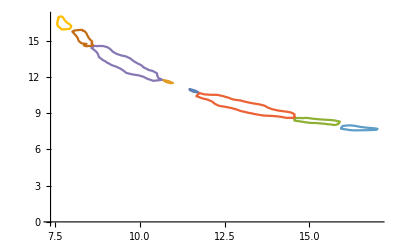

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

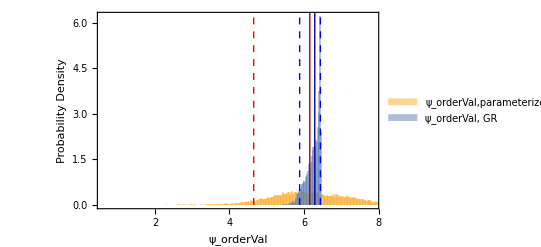

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.475, 0.525}

实际使用的 GR 概率区间上下界: {6.27675, 6.30255}

实际使用的 Param 概率区间上下界: {6.0847, 6.22077}

GR下界: 点数=27 | 平均误差=3.28955×10^-16

GR上界: 点数=27 | 平均误差=1.31582×10^-16

Param下界: 点数=27 | 平均误差=8.22387×10^-16

Param上界: 点数=27 | 平均误差=8.88178×10^-16

chi1L取值：0.614549

chi2L取值：0.529968

=====================================================

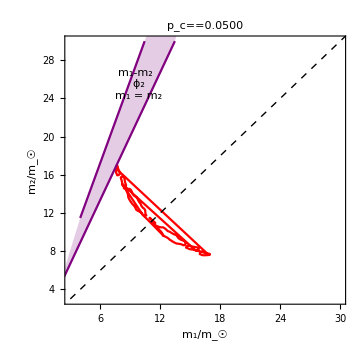

```mathematica
probability=prob;
probability=0.05;

PlotInversion[p,probability,3,30,1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3,4,5,6,7,8}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0198};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 22184 + 镜像 22184

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0198}，共 2 条

第一条前3点：{{11.8013,11.2979},{11.8492,11.2623},{11.8922,11.2296}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.509821

可信水平百分比：50.9821%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.509821

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

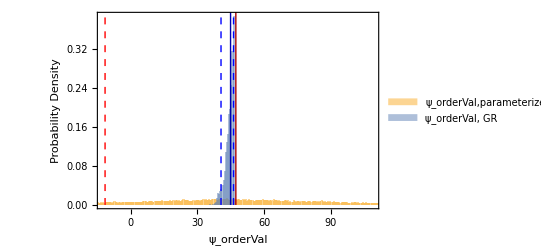

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.48825, 0.51175}

实际使用的 GR 概率区间上下界: {44.8374, 44.9419}

实际使用的 Param 概率区间上下界: {46.2448, 48.34}

GR下界: 点数=27 | 平均误差=4.73695×10^-15

GR上界: 点数=27 | 平均误差=5.26328×10^-15

Param下界: 点数=27 | 平均误差=5.26328×10^-16

Param上界: 点数=27 | 平均误差=2.09416

chi1L取值：0.569676

chi2L取值：0.495363

=====================================================

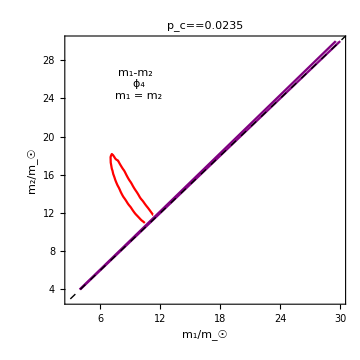

```mathematica
probability=prob;
probability=0.0235;

PlotInversion[p,probability,3,30,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.032};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 37274 + 镜像 37274

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.032}，共 6 条

第一条前3点：{{14.5964,8.63449},{14.625,8.62161},{14.6491,8.70281}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

=====  =====

包含片段数：6 (合并模式: False)

区域内总积分值：0.0707254

可信水平百分比：7.07254%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.0707254

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

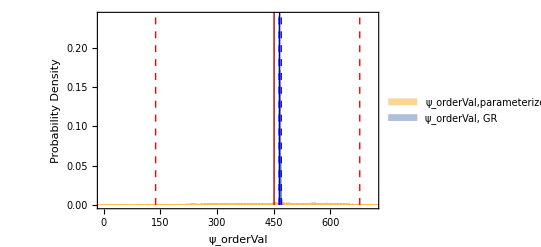

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.464637, 0.535363}

实际使用的 GR 概率区间上下界: {465.933, 466.248}

实际使用的 Param 概率区间上下界: {435.876, 465.84}

GR下界: 点数=185 | 平均误差=3.07262×10^-14

GR上界: 点数=185 | 平均误差=5.68434×10^-14

Param下界: 点数=185 | 平均误差=28.8807

Param上界: 点数=185 | 平均误差=2.05865×10^-14

chi1L取值：0.556081

chi2L取值：0.549942

=====================================================

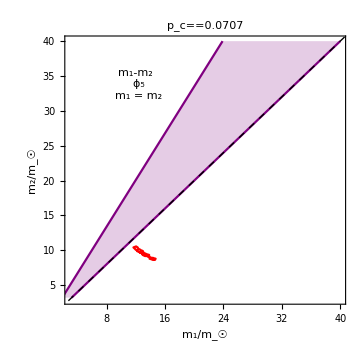

```mathematica
probability=prob;
(*probability=0.1302;*)

PlotInversion[p,probability,3,40,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0276};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 33798 + 镜像 33798

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0276}，共 2 条

第一条前3点：{{9.27927,12.8862},{9.29756,12.8396},{9.32587,12.8021}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.113796

可信水平百分比：11.3796%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.113796

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

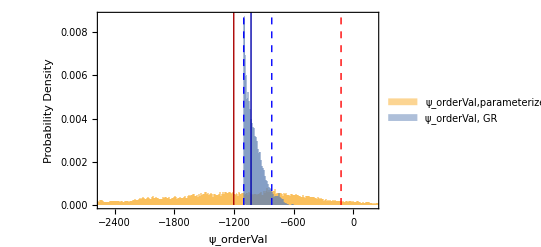

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.443102, 0.556898}

实际使用的 GR 概率区间上下界: {-1041.9, -1014.73}

实际使用的 Param 概率区间上下界: {-1307.96, -1089.6}

GR下界: 点数=370 | 平均误差=1.25363×10^-13

GR上界: 点数=370 | 平均误差=1.57933×10^-13

Param下界: 点数=370 | 平均误差=203.836

Param上界: 点数=370 | 平均误差=1.35195×10^-13

chi1L取值：0.531846

chi2L取值：0.440716

=====================================================

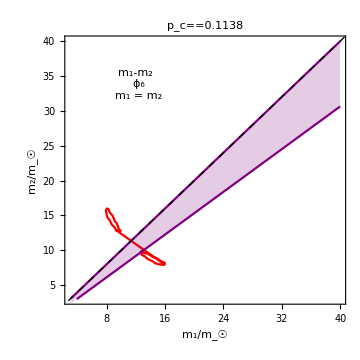

```mathematica
probability=prob;
(*probability=0.15;*)

PlotInversion[p,probability,3,40,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,30},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0285};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,30}

输入q范围：{1,5}

m1范围：{3.4461,81.7221}

m2范围：{1.63444,34.461}

对称数据：原始 32222 + 镜像 32222

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 81.7221} × {1.63444, 81.7221}

等高线值：{0.0285}，共 4 条

第一条前3点：{{15.811,7.99559},{15.8277,8.00065},{15.8464,8.05265}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.137175

可信水平百分比：13.7175%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.137175

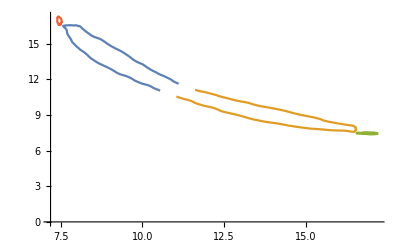

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

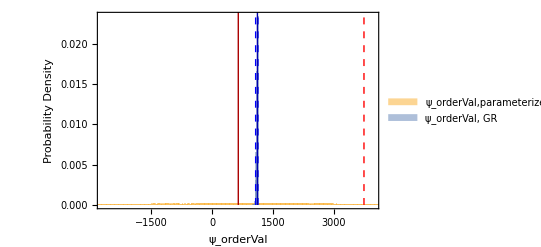

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.431412, 0.568588}

实际使用的 GR 概率区间上下界: {1115.16, 1121.4}

实际使用的 Param 概率区间上下界: {274.01, 1048.09}

GR下界: 点数=270 | 平均误差=1.19582×10^-13

GR上界: 点数=270 | 平均误差=4.0422×10^-14

Param下界: 点数=270 | 平均误差=679.505

Param上界: 点数=270 | 平均误差=1.26319×10^-13

chi1L取值：0.552261

chi2L取值：0.528894

=====================================================

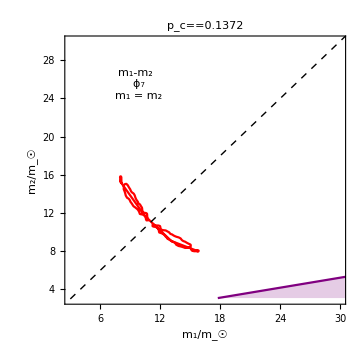

```mathematica
probability=prob;
(*probability=0.15;*)
(*0.32*)
PlotInversion[p,probability,3,30,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3,4}]
```

# utils